```mathematica
Series[Sqrt[1-x^2],{x,0.5,20}]
```

0.866025-0.57735 (x-0.5)-0.7698 (x-0.5)^2-0.5132 (x-0.5)^3-0.684267 (x-0.5)^4-0.912356 (x-0.5)^5-1.36853 (x-0.5)^6-2.12883 (x-0.5)^7-3.44668 (x-0.5)^8-5.72194 (x-0.5)^9-9.70176 (x-0.5)^10-16.7203 (x-0.5)^11-29.2087 (x-0.5)^12-51.6003 (x-0.5)^13-92.0286 (x-0.5)^14-165.475 (x-0.5)^15-299.646 (x-0.5)^16-545.973 (x-0.5)^17-1000.24 (x-0.5)^18-1841.39 (x-0.5)^19-3404.65 (x-0.5)^20+O[x-0.5]^21

```mathematica
Plot[Evaluate[Normal[%5]],{x,-8,8}]
```

-Graphics-

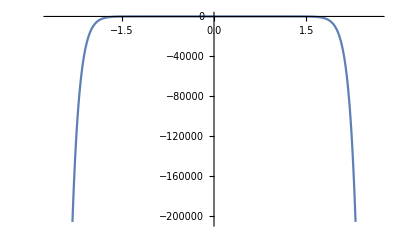

```mathematica
Plot[Evaluate[Normal[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128-(7 x^10)/256-(21 x^12)/1024-(33 x^14)/2048-(429 x^16)/32768-(715 x^18)/65536-(2431 x^20)/262144+O[x]^21]],{x,-2.6568446566202857,2.6568446566202857}]
```

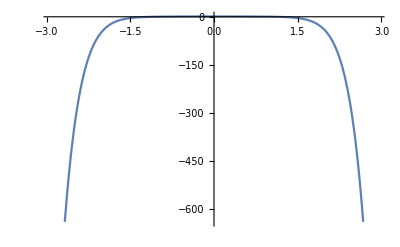

```mathematica
Plot[Evaluate[Normal[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128-(7 x^10)/256+O[x]^11]],{x,-2.9277002188455996,2.9277002188455996}]
```

```mathematica
Series[x,{x,10,4}]
```

10+(x-10)+O[x-10]^5

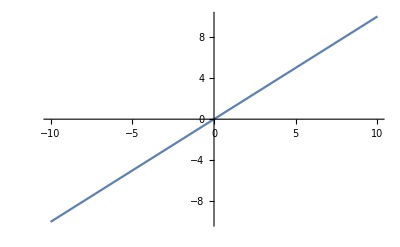

```mathematica
Plot[Evaluate[Normal[10+(x-10)+O[x-10]^5]],{x,-10,10}]
```

```mathematica
Plot[Evaluate[Normal[x+O[x]^5]],{x,-10,10}]
```

-Graphics-

```mathematica
Plot[Evaluate[Normal[2+(x-2)+O[x-2]^5]],{x,-10,10}]
```

-Graphics-

```mathematica
Plot[Evaluate[Normal[a+(x-a)+O[x-a]^5]],{x,-10,10}]
```

-Graphics-

```mathematica
10+(x-10)
```

x

```mathematica
Series[Exp[x^2],{x,2,5}]
```

ⅇ^4+4 ⅇ^4 (x-2)+9 ⅇ^4 (x-2)^2+44/3 ⅇ^4 (x-2)^3+115/6 ⅇ^4 (x-2)^4+106/5 ⅇ^4 (x-2)^5+O[x-2]^6

```mathematica
Plot[Evaluate[Normal[ⅇ^4+4 ⅇ^4 (x-2)+9 ⅇ^4 (x-2)^2+44/3 ⅇ^4 (x-2)^3+115/6 ⅇ^4 (x-2)^4+106/5 ⅇ^4 (x-2)^5+O[x-2]^6]],{x,-54.575471698113205,54.575471698113205}]
```

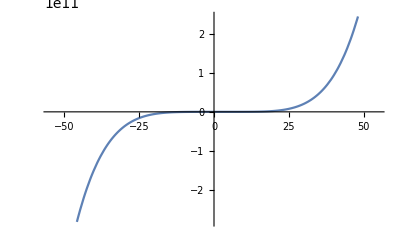
```mathematica
-Graphics-Plot[Exp[x^2],{x,-5,5}]
```

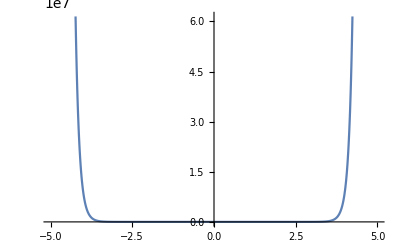
-Graphics- -Graphics-

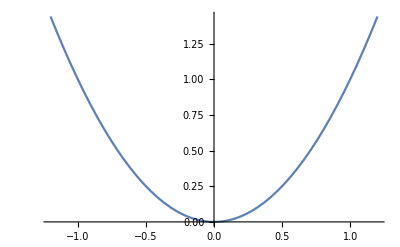

```mathematica
Plot[Evaluate[Normal[4+4 (x-2)+(x-2)^2+O[x-2]^6]],{x,-1.2,1.2}]
```

```mathematica
Plot[Exp[x^2],{x,-5,5}]
```

-Graphics-

```mathematica
Series[Exp[x^2],{x,0,10}]
```

1+x^2+x^4/2+x^6/6+x^8/24+x^10/120+O[x]^11

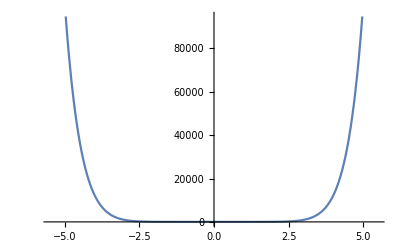

```mathematica
Plot[Evaluate[Normal[1+x^2+x^4/2+x^6/6+x^8/24+x^10/120+O[x]^11]],{x,-5.477225575051661,5.477225575051661}]
```

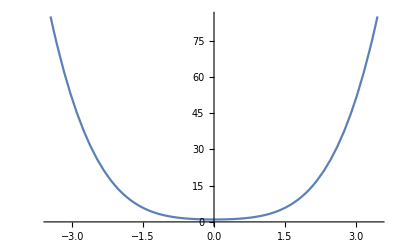

```mathematica
Plot[Evaluate[Normal[1+x^2+x^4/2+O[x]^6]],{x,-3.464101615137755,3.464101615137755}]
```

```mathematica
D[Exp[x^2],x]
```

2 ⅇ^(x^2) x

```mathematica
Plot[2 ⅇ^(x^2) x,{x,-10.392304845413262,10.392304845413262}]
```

-Graphics-

```mathematica
Series[Exp[x^2],{x,4,10}]
```

ⅇ^16+8 ⅇ^16 (x-4)+33 ⅇ^16 (x-4)^2+280/3 ⅇ^16 (x-4)^3+1219/6 ⅇ^16 (x-4)^4+1812/5 ⅇ^16 (x-4)^5+49583/90 ⅇ^16 (x-4)^6+230948/315 ⅇ^16 (x-4)^7+146311/168 ⅇ^16 (x-4)^8+(2656561 ⅇ^16 (x-4)^9)/2835+(14965991 ⅇ^16 (x-4)^10)/16200+O[x-4]^11

```mathematica
Plot[Evaluate[Normal[ⅇ^16+8 ⅇ^16 (x-4)+33 ⅇ^16 (x-4)^2+280/3 ⅇ^16 (x-4)^3+1219/6 ⅇ^16 (x-4)^4+1812/5 ⅇ^16 (x-4)^5+49583/90 ⅇ^16 (x-4)^6+230948/315 ⅇ^16 (x-4)^7+146311/168 ⅇ^16 (x-4)^8+(2656561 ⅇ^16 (x-4)^9)/2835+(14965991 ⅇ^16 (x-4)^10)/16200+O[x-4]^11]],{x,-233.9140621273545,233.9140621273545}]
```

-Graphics-

```mathematica
Plot[Evaluate[Normal[1+x^2+x^4/2+x^6/6+x^8/24+x^10/120+O[x]^11]],{x,-5.477225575051661,5.477225575051661}]
```

-Graphics-

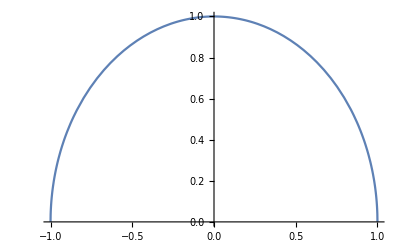

```mathematica
Plot[
Sqrt[1-x^2],{x,-1,1}
]
```

```mathematica
Integrate[Integrate[Sqrt[1],{y,0,Sqrt[1-x^2]}]1,{x,0,1}]
```

π/4

```mathematica
F1=Series[Sqrt[1-x^2],{x,0.5,10}] //Normal
```

0.866025-0.57735 (-0.5+x)-0.7698 (-0.5+x)^2-0.5132 (-0.5+x)^3-0.684267 (-0.5+x)^4-0.912356 (-0.5+x)^5-1.36853 (-0.5+x)^6-2.12883 (-0.5+x)^7-3.44668 (-0.5+x)^8-5.72194 (-0.5+x)^9-9.70176 (-0.5+x)^10

```mathematica
Series[Sqrt[1-x^2],{x,1,15}]
```

(√2 √(1-x) √(x-1))/(√(-1+x))+(√(1-x) (x-1)^(3/2))/(2 √2 √(-1+x))-(√(1-x) (x-1)^(5/2))/(16 (√2 √(-1+x)))+(√(1-x) (x-1)^(7/2))/(64 √2 √(-1+x))-(5 √(1-x) (x-1)^(9/2))/(1024 (√2 √(-1+x)))+(7 √(1-x) (x-1)^(11/2))/(4096 √2 √(-1+x))-(21 √(1-x) (x-1)^(13/2))/(32768 (√2 √(-1+x)))+(33 √(1-x) (x-1)^(15/2))/(131072 √2 √(-1+x))-(429 √(1-x) (x-1)^(17/2))/(4194304 (√2 √(-1+x)))+(715 √(1-x) (x-1)^(19/2))/(16777216 √2 √(-1+x))-(2431 √(1-x) (x-1)^(21/2))/(134217728 (√2 √(-1+x)))+(4199 √(1-x) (x-1)^(23/2))/(536870912 √2 √(-1+x))-(29393 √(1-x) (x-1)^(25/2))/(8589934592 (√2 √(-1+x)))+(52003 √(1-x) (x-1)^(27/2))/(34359738368 √2 √(-1+x))-(185725 √(1-x) (x-1)^(29/2))/(274877906944 (√2 √(-1+x)))+O[x-1]^(31/2)

```mathematica
Normal[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128-(7 x^10)/256-(21 x^12)/1024-(33 x^14)/2048+O[x]^16]
```

```mathematica
F1=1-x^2/2-x^4/8-x^6/16-(5 x^8)/128-(7 x^10)/256-(21 x^12)/1024-(33 x^14)/2048
```

1-x^2/2-x^4/8-x^6/16-(5 x^8)/128-(7 x^10)/256-(21 x^12)/1024-(33 x^14)/2048

```mathematica
Normal[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128+O[x]^10]
```

```mathematica
Integrate[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128,{x,0,1}]
```

32057/40320

```mathematica
N[32057/40320]
```

0.795064

```mathematica
Pi/4//N
```

0.785398

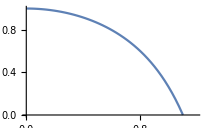

```mathematica
Plot[1-x^2/2-x^4/8-x^6/16-(5 x^8)/128,{x,0,1.2},PlotRange->{0,1}]
```

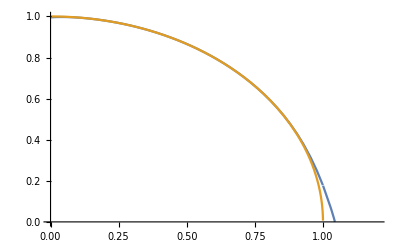

```mathematica
Plot[{F1,Sqrt[1-x^2]},{x,0,1.2},PlotRange->{0,1}]
```

```mathematica
Plot[F1,{x,0,1.2},PlotRange->{0,1}]
```

-Graphics-

```mathematica
Normal[1-x^2/2-x^4/8+O[x]^5]
```

1-x^2/2-x^4/8

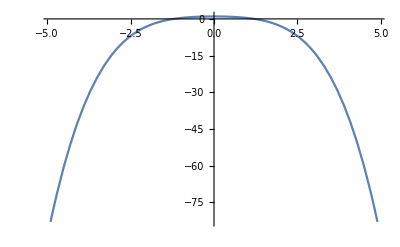

```mathematica
Plot[1-x^2/2-x^4/8,{x,-4.898979485566356,4.898979485566356}]
```